```mathematica
SetDirectory[NotebookDirectory[]];
FileNames[]
```

{1200.nb,1200_upravene.nb,1400.nb,1500.nb,1600.nb,1800.nb,2000.nb,final-NG-1200-100SK-27BTDC.pdf,NG-1200-100SK-27BTDC.TXT,NG-1400-100SK-27BTDC.TXT,NG-1500-100SK-27BTDC.TXT,NG-1600-100SK-27BTDC.TXT,NG-1800-100SK-27BTDC.TXT,NG-2000-100SK-27BTDC.TXT,piatystlpec-NG-1200-100SK-27BTDC.TXT.txt,piatystlpec-NG-1200-100SK-27BTDC.TXT.xls,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls,tretistlpec-NG-1200-100SK-27BTDC.TXT.txt,tretistlpec-NG-1200-100SK-27BTDC.TXT.xls}

```mathematica
subor="NG-1400-100SK-27BTDC.TXT";
```

```mathematica
b=ReadList[subor,Table[Number,{5}]];
```

```mathematica
prvystlpec=b[[All,1]];
druhystlpec=b[[All,2]];
tretistlpec=b[[All,3]];
stvrtystlpec=b[[All,4]];
piatystlpec=b[[All,5]];
```

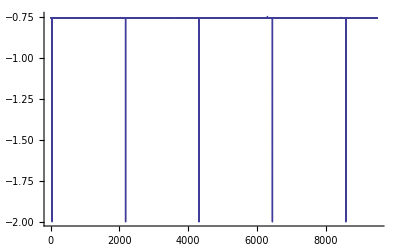

```mathematica
ListLinePlot[druhystlpec[[1;;9500;;1]],PlotRange->All]
```

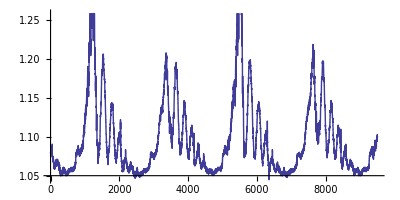

```mathematica
ListLinePlot[tretistlpec[[1;;9500;;1]],AspectRatio->0.5]
```

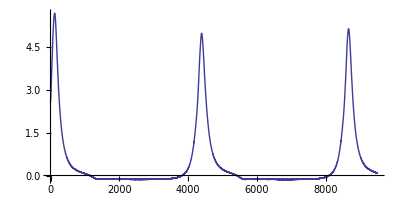

```mathematica
ListLinePlot[stvrtystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

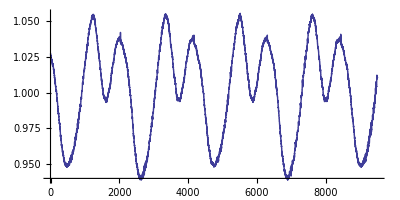

```mathematica
ListLinePlot[piatystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

```mathematica
Length[prvystlpec]
```

1048576

```mathematica
pom3={};
Do[
If[druhystlpec[[i]]<-1.8,AppendTo[pom3, i]],{i,1,Length[druhystlpec]}];
pom4={};
Do[
If[pom3[[i+1]]-pom3[[i]]>10,AppendTo[pom4,pom3[[i]]]],{i,1, Length[pom3]-1}];
pom4
```

{49,2182,4315,6449,8582,10716,12849,14983,17117,19250,21383,23516,25650,27784,29918,32052,34185,36318,38451,40585,42717,44851,46984,49117,51249,53382,55515,57648,59780,61913,64045,66178,68310,70443,72577,74711,76844,78977,81111,83245,85378,87511,89645,91778,93912,96045,98179,100312,102446,104580,106713,108847,110980,113112,115245,117378,119510,121643,123776,125909,128042,130175,132308,134441,136574,138708,140841,142974,145107,147241,149373,151507,153640,155773,157906,160039,162172,164306,166439,168572,170704,172837,174970,177103,179235,181368,183501,185634,187766,189899,192031,194164,196295,198428,200559,202692,204824,206957,209089,211221,213354,215487,217619,219753,221886,224019,226152,228286,230419,232552,234685,236819,238952,241085,243218,245351,247483,249616,251749,253881,256014,258146,260279,262412,264544,266676,268809,270941,273074,275207,277339,279472,281605,283737,285870,288003,290136,292269,294401,296534,298667,300799,302932,305064,307196,309328,311460,313593,315725,317858,319990,322122,324254,326387,328519,330652,332784,334917,337050,339183,341316,343449,345582,347715,349848,351981,354114,356248,358381,360516,362649,364783,366917,369051,371185,373319,375454,377588,379722,381856,383990,386123,388256,390389,392522,394656,396788,398921,401054,403186,405318,407450,409582,411714,413846,415977,418109,420242,422374,424507,426639,428772,430905,433037,435170,437303,439436,441569,443703,445837,447970,450104,452237,454371,456504,458637,460770,462903,465037,467170,469303,471436,473569,475703,477836,479970,482103,484237,486370,488504,490638,492772,494905,497039,499172,501306,503439,505573,507707,509841,511975,514109,516243,518376,520510,522644,524777,526910,529043,531176,533309,535442,537575,539709,541842,543975,546108,548241,550373,552506,554639,556772,558904,561037,563170,565302,567435,569568,571701,573834,575966,578099,580232,582365,584498,586632,588765,590899,593032,595165,597298,599431,601564,603697,605831,607964,610097,612231,614364,616497,618630,620763,622896,625028,627161,629294,631426,633559,635691,637824,639957,642089,644222,646355,648487,650620,652752,654885,657018,659151,661284,663417,665550,667683,669816,671949,674082,676214,678347,680480,682613,684746,686879,689011,691144,693277,695409,697542,699675,701809,703941,706074,708207,710340,712473,714607,716740,718873,721007,723140,725273,727406,729539,731671,733804,735936,738069,740201,742334,744467,746600,748733,750866,753000,755133,757266,759398,761531,763664,765798,767931,770066,772200,774335,776469,778604,780739,782873,785008,787143,789278,791412,793547,795681,797816,799950,802084,804217,806351,808484,810618,812751,814884,817017,819150,821282,823415,825549,827682,829815,831947,834080,836212,838345,840477,842609,844742,846875,849008,851141,853274,855406,857539,859672,861805,863938,866071,868204,870336,872469,874602,876735,878868,881001,883134,885266,887399,889533,891665,893799,895931,898065,900198,902332,904466,906600,908734,910868,913002,915135,917268,919402,921535,923669,925802,927936,930069,932203,934336,936470,938603,940735,942868,945001,947133,949267,951400,953533,955667,957800,959933,962066,964199,966332,968466,970599,972732,974865,976999,979132,981265,983398,985530,987663,989795,991928,994060,996193,998325,1000458,1002591,1004723,1006855,1008988,1011121,1013253,1015386,1017519,1019651,1021784,1023916,1026050,1028183,1030316,1032449,1034582,1036716,1038849,1040982,1043116,1045249}

```mathematica
Length[pom4]
```

491

```mathematica
cyklus={};
Table[AppendTo[cyklus,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus//Length
```

244

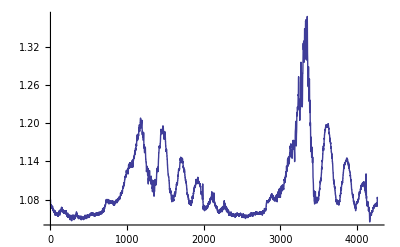
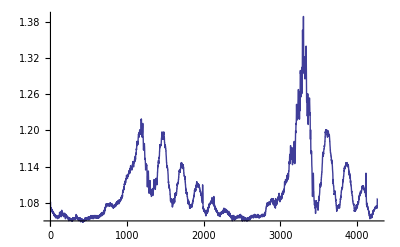
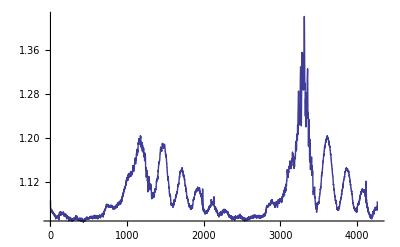
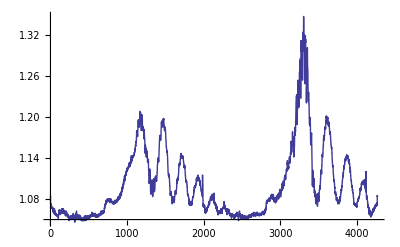
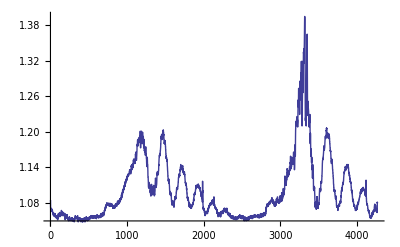
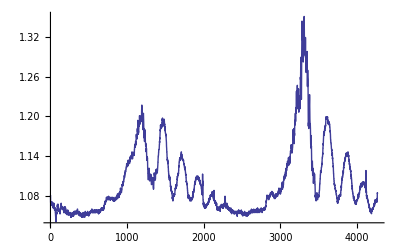
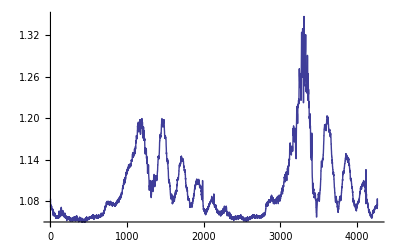
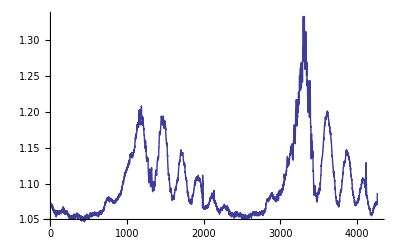

```mathematica
Table[ListLinePlot[cyklus[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]
```

{4268,4268,4268,4268,4267,4269,4269,4267,4268,4267,4267,4266,4267,4266,4266,4266,4269,4267,4269,4267,4268,4268,4268,4269,4268,4266,4267,4266,4267,4267,4267,4268,4267,4268,4267,4267,4267,4268,4267,4266,4267,4266,4267,4266,4266,4265,4265,4266,4265,4267,4267,4267,4268,4267,4268,4267,4267,4266,4266,4266,4267,4265,4266,4267,4266,4266,4267,4267,4266,4266,4266,4265,4266,4266,4265,4266,4266,4266,4267,4267,4267,4267,4268,4269,4268,4269,4269,4270,4269,4268,4267,4268,4266,4266,4265,4265,4264,4266,4266,4266,4266,4267,4267,4269,4268,4268,4267,4267,4268,4267,4268,4268,4268,4268,4269,4268,4268,4268,4269,4269,4268,4269,4267,4267,4267,4268,4267,4267,4266,4267,4266,4266,4267,4267,4266,4267,4268,4268,4267,4267,4267,4268,4268,4267,4267,4266,4267,4266,4266,4266,4267,4266,4266,4267,4267,4267,4267,4266,4267,4267,4266,4267,4266,4268,4266,4267,4268,4267,4268,4267,4266,4266,4266,4267,4267,4268,4267,4266,4268,4269,4270,4270,4270,4271,4270,4270,4270,4268,4268,4268,4267,4266,4268,4267,4266,4266,4265,4267,4267,4266,4267,4267,4267,4266,4267,4267,4266,4268,4267,4267,4268,4269,4269,4268,4268,4268,4268,4268,4268,4266,4267,4267,4267,4268,4267,4267,4268,4267,4268,4267,4266,4266,4266,4266,4266,4266,4266,4267,4266,4267,4267,4267,4268,4268}

```mathematica
pom5=Min[Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]];
pom6=Table[Take[cyklus[[i]],pom5],{i,1,Length[cyklus]}];
```

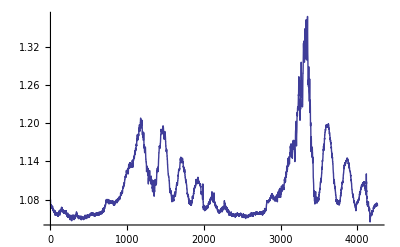
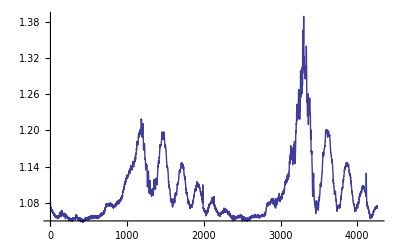
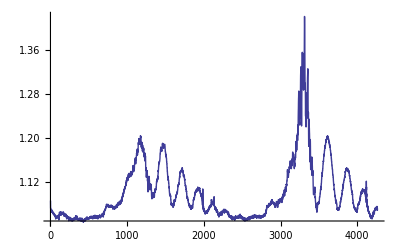
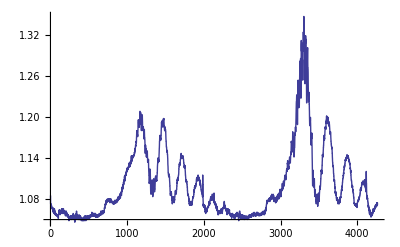
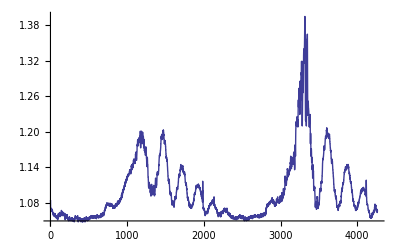
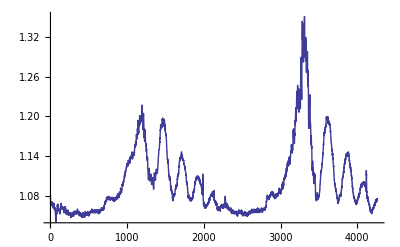
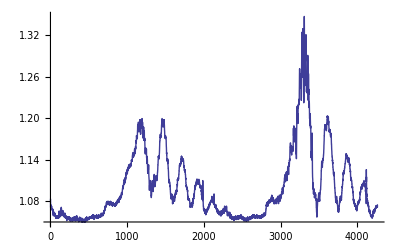
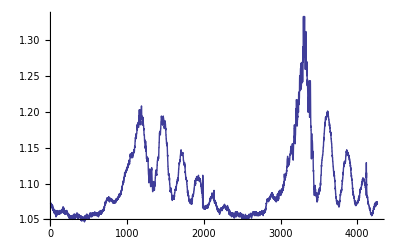

```mathematica
Table[ListLinePlot[pom6[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[pom6]//Dimensions
```

{4264,244}

```mathematica
priemernehodnotydruhystlpec=Table[Mean[pom6[[All,i]]],{i,1,4264}];
```

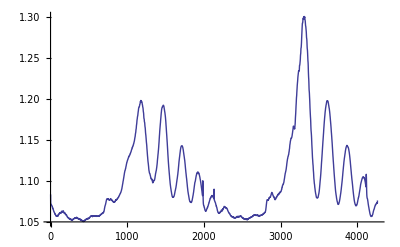

```mathematica
ListLinePlot[priemernehodnotydruhystlpec]
```

```mathematica
cyklus3={};
cyklus4={};
cyklus5={};
Table[AppendTo[cyklus3,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus4,stvrtystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus5,piatystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus3//Length
```

244

```mathematica
Table[ListLinePlot[cyklus3[[i]],PlotRange->All],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

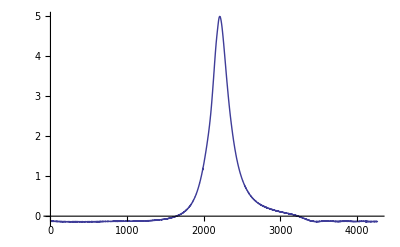
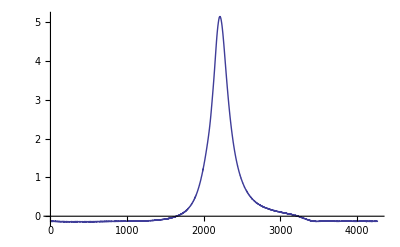
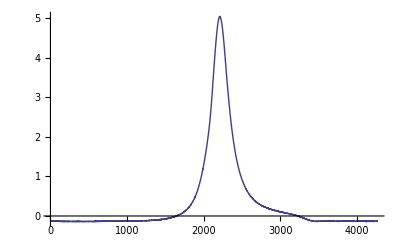
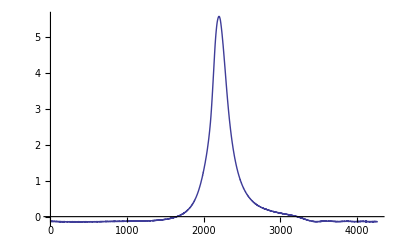
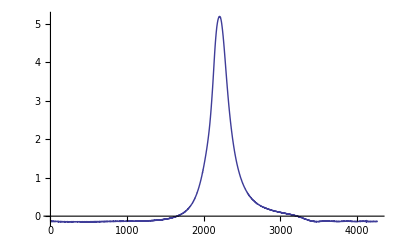
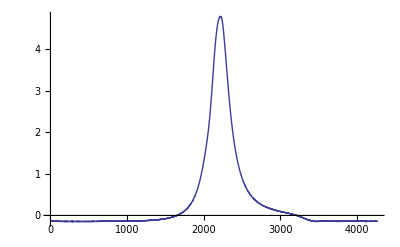
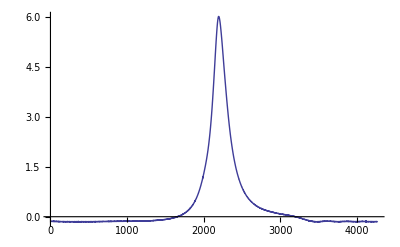
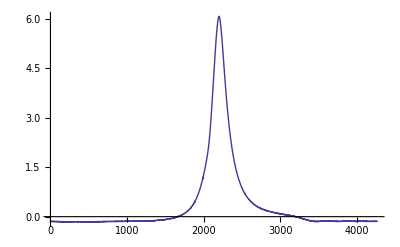

```mathematica
Table[ListLinePlot[cyklus4[[i]],PlotRange->All],{i,1,10}]
```

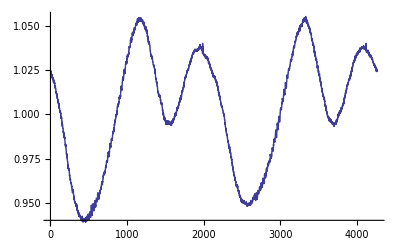
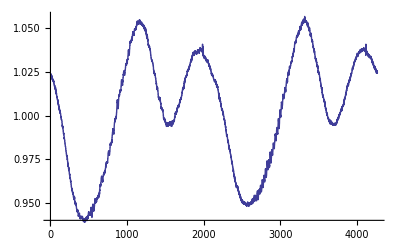
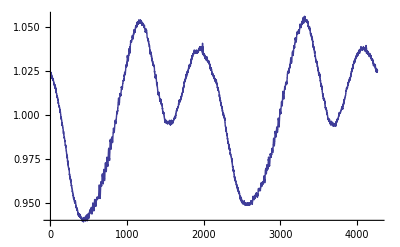
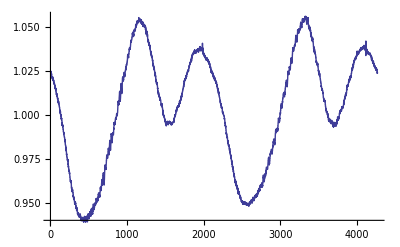
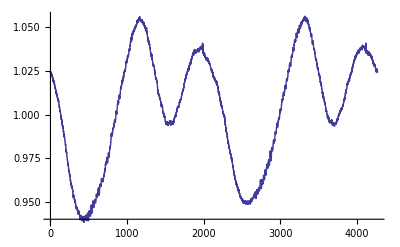
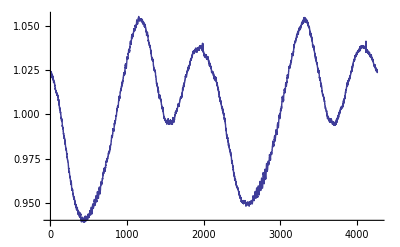
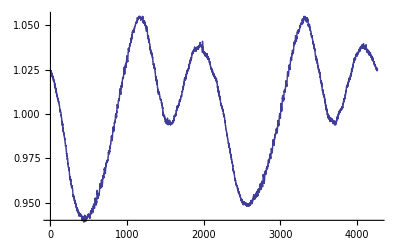
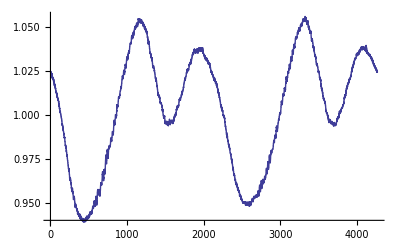

```mathematica
Table[ListLinePlot[cyklus5[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus3[[i]]],{i,1,Length[cyklus]}]
```

{4268,4268,4268,4268,4267,4269,4269,4267,4268,4267,4267,4266,4267,4266,4266,4266,4269,4267,4269,4267,4268,4268,4268,4269,4268,4266,4267,4266,4267,4267,4267,4268,4267,4268,4267,4267,4267,4268,4267,4266,4267,4266,4267,4266,4266,4265,4265,4266,4265,4267,4267,4267,4268,4267,4268,4267,4267,4266,4266,4266,4267,4265,4266,4267,4266,4266,4267,4267,4266,4266,4266,4265,4266,4266,4265,4266,4266,4266,4267,4267,4267,4267,4268,4269,4268,4269,4269,4270,4269,4268,4267,4268,4266,4266,4265,4265,4264,4266,4266,4266,4266,4267,4267,4269,4268,4268,4267,4267,4268,4267,4268,4268,4268,4268,4269,4268,4268,4268,4269,4269,4268,4269,4267,4267,4267,4268,4267,4267,4266,4267,4266,4266,4267,4267,4266,4267,4268,4268,4267,4267,4267,4268,4268,4267,4267,4266,4267,4266,4266,4266,4267,4266,4266,4267,4267,4267,4267,4266,4267,4267,4266,4267,4266,4268,4266,4267,4268,4267,4268,4267,4266,4266,4266,4267,4267,4268,4267,4266,4268,4269,4270,4270,4270,4271,4270,4270,4270,4268,4268,4268,4267,4266,4268,4267,4266,4266,4265,4267,4267,4266,4267,4267,4267,4266,4267,4267,4266,4268,4267,4267,4268,4269,4269,4268,4268,4268,4268,4268,4268,4266,4267,4267,4267,4268,4267,4267,4268,4267,4268,4267,4266,4266,4266,4266,4266,4266,4266,4267,4266,4267,4267,4267,4268,4268}

```mathematica
pom5=Min[Table[Length[cyklus3[[i]]],{i,1,Length[cyklus3]}]];
cyklus3orezany=Table[Take[cyklus3[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus4orezany=Table[Take[cyklus4[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus5orezany=Table[Take[cyklus5[[i]],pom5],{i,1,Length[cyklus3]}];
```

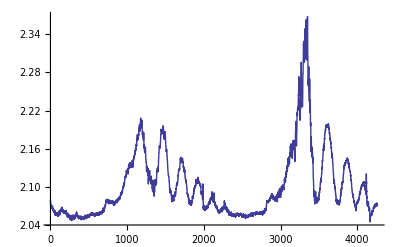
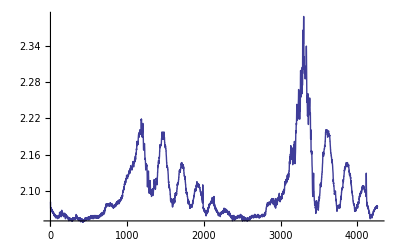
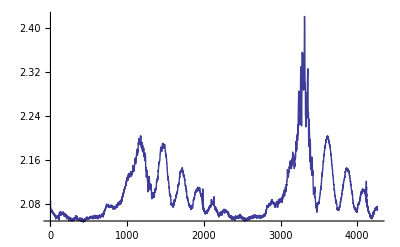
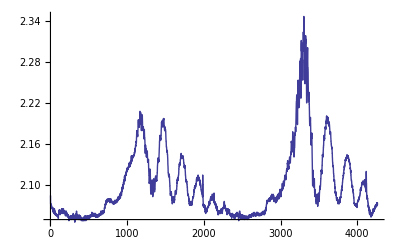
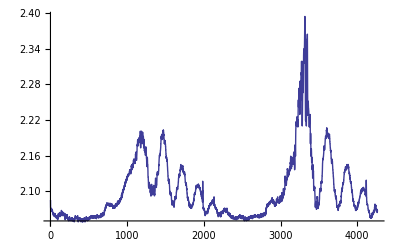
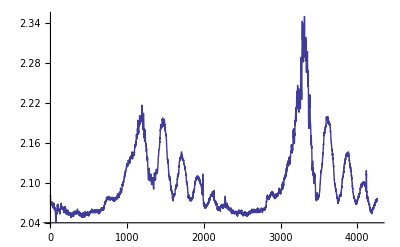
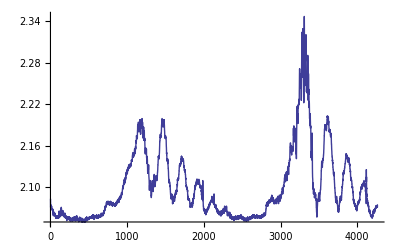
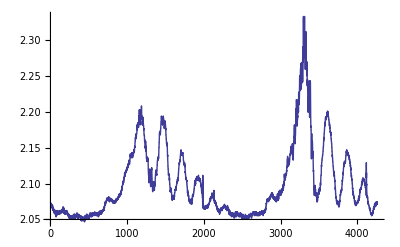

```mathematica
Table[ListLinePlot[cyklus3orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

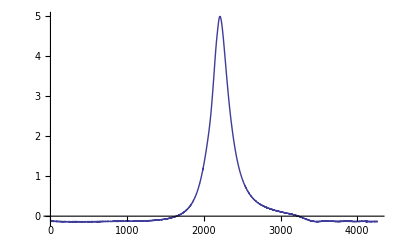
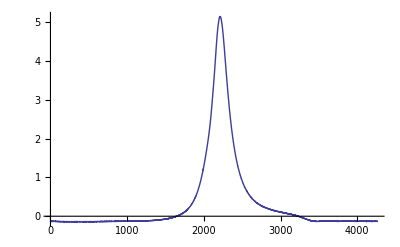
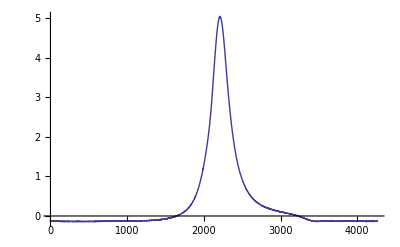
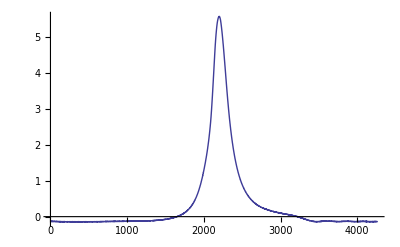
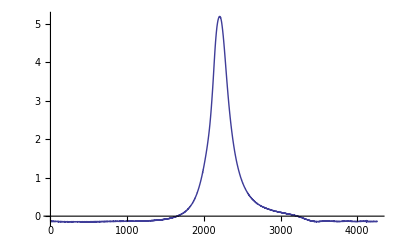
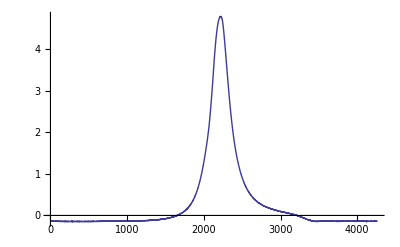
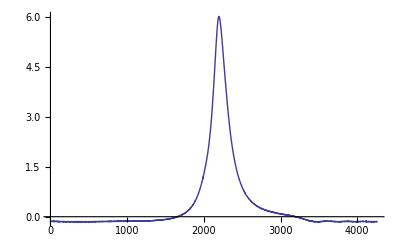
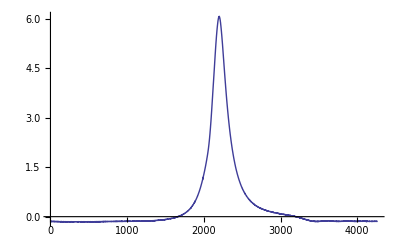

```mathematica
Table[ListLinePlot[cyklus4orezany[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[cyklus3orezany]//Dimensions
```

{4264,244}

```mathematica
priemernehodnoty3stlpec=Table[Mean[cyklus3orezany[[All,i]]],{i,1,4264}];
priemernehodnoty4stlpec=Table[Mean[cyklus4orezany[[All,i]]],{i,1,4264}];
priemernehodnoty5stlpec=Table[Mean[cyklus5orezany[[All,i]]],{i,1,4264}];
```

```mathematica
Length[priemernehodnoty4stlpec]
```

4264

```mathematica
k=0;
x=Table[k=k+720/Length[priemernehodnoty4stlpec]//N,{Length[priemernehodnoty4stlpec]}];
```

```mathematica
obr3=ListLinePlot[priemernehodnoty3stlpec]
```

-Graphics-

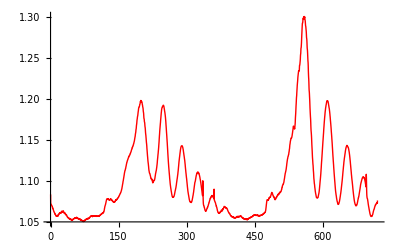

```mathematica
dataobr3=Transpose@{x,priemernehodnoty3stlpec};
obr3aa=ListLinePlot[dataobr3,PlotStyle->Red]
```

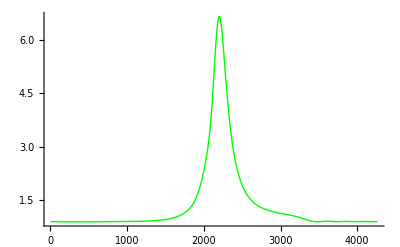

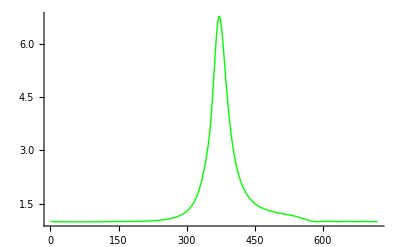

```mathematica
obr4=ListLinePlot[priemernehodnoty4stlpec+1.0335, PlotStyle->Green,PlotRange->All]
priemernehodnoty4stlpecnove=priemernehodnoty4stlpec+1.1335;
dataobr4=Transpose@{x,priemernehodnoty4stlpecnove};
obr1400va=ListLinePlot[dataobr4,PlotStyle->Green,PlotRange->All]
```

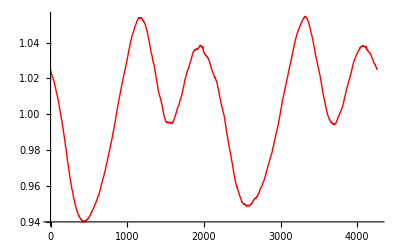

```mathematica
obr5=ListLinePlot[priemernehodnoty5stlpec,PlotStyle->Red]
```

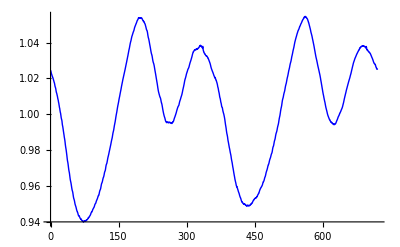

```mathematica
dataobr5=Transpose@{x,priemernehodnoty5stlpec};
obr1400a=ListLinePlot[dataobr5,PlotStyle->Blue]
```

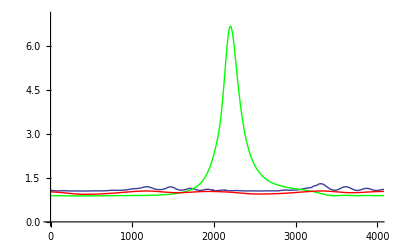

```mathematica
Show[{obr3,obr4,obr5},PlotRange->{{0,4000},{0,7}},AxesOrigin->{0,0}]
```

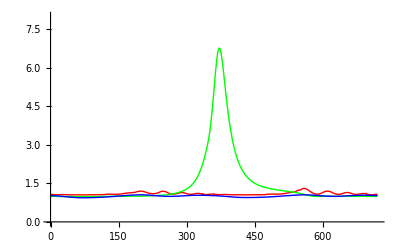

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0,8}},AxesOrigin->{0,0}]
```

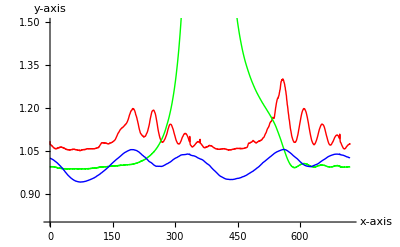

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},LabelStyle->(FontSize->14),AxesLabel->{"x-axis","y-axis"}]
```

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},PlotRange->{{-3,0},{0,1}},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

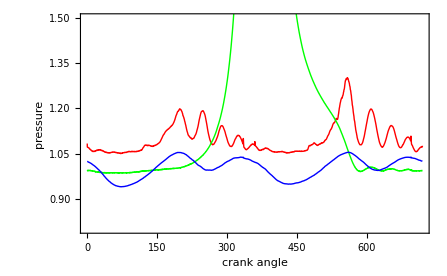

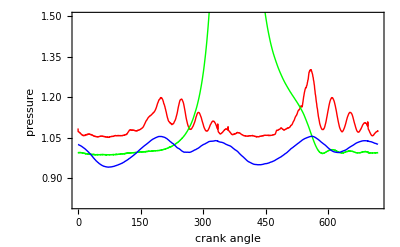

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

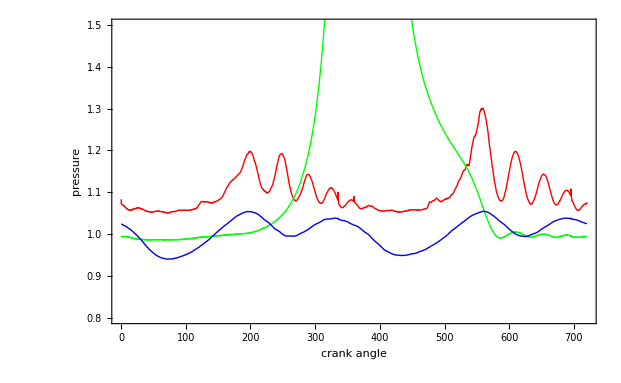

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```